# Teaching and learning with smart phone and Mathematica

Roger Yu

Mentor: Paul Abbott

## Introduction

Mathematical literacy has become a familiar term in higher education and computational thinking as a way of communicating has also propelled its way into the main stream of our society. As a professional in the area of higher education, I am obligated to make a pathway for our students in all areas of studies to immerse themselves into this technological shift.

This project aims at combining the usages of smart phones and Wolfram Language in the delivery of one of our core courses. The core course  considered here is required for all freshmen students. Approximately 30 sections of the course is offered in each semester and each section has about 30 students coming from all  disciplines ranging from engineering, sciences, math, to arts, and architecture.

Currently, we are already using smart phones as a tool, in some cases the only tool, in hands-on activities or experiments. This project integrates Mathematica with the application of smart phones so to encourage students to make comparisons between theory and observation. Since all students are required to use smart phone for his/her all course works, the Wolfram Cloud App will be heavily used for activities and interactions. By doing so, Wolfram Language becomes much more personal and powerful.

Many on-line resources have become available for students to have a jump start in using Mathematica. The following video clip published by Wolfram University is particularly helpful in initial training so we will use it as a teaching tool.

## Integration of smart phones and Mathematica

In the following, we will discuss a few examples of engaging practices that each student will work on his/her own. All of these examples can be chosen by courses at different levels or disciplines.

### Example 1: Voice recognition and analysis

This example uses AudioCapture to help students capture his/her own voice then analyze it at a basic level. The analysis and especially the  visualization of student’s own voice would serve as an effective draw of their interests to Mathematica.

```mathematica
studentsvoice=AudioCapture[]
```

Spectrogram plots the spectrogram of the captured audio signal:

```mathematica
Spectrogram[studentsvoice]
```

-Graphics-

AudioPlot plots the waveform of of the captured audio signal:

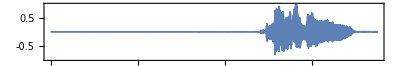

```mathematica
AudioPlot[studentsvoice]
```

AudioLocalMeasurements displays the frequencies of the formants of the signal:

```mathematica
studentstimeseries=AudioLocalMeasurements[studentsvoice,"Formants"]
```

TimeSeries[…]

Display the frequency time series using ListPlot:

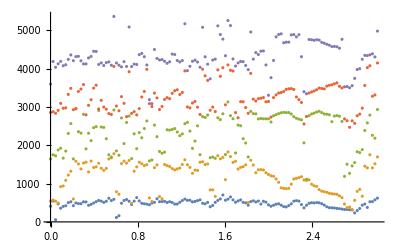

```mathematica
ListPlot[studentstimeseries]
```

Alternatively, use ListLinePlot:

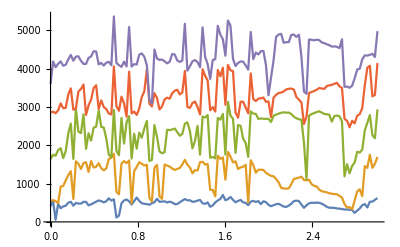

```mathematica
ListLinePlot[studentstimeseries]
```

Use AudioLocalMeasurements to compute the maximum values of the average channel values:

```mathematica
studentsmax=AudioLocalMeasurements[studentsvoice, "Max"]
```

TimeSeries[…]

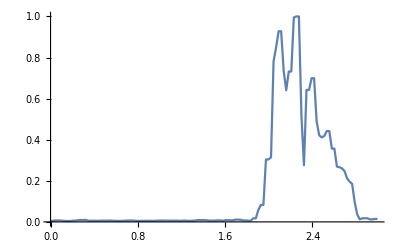

```mathematica
ListLinePlot[studentsmax]
```

### Example 2: Analysis of an MP3 audio file

This example encourages students to pick and choose samples of audio signals from the Mathematica data base “ExampleData” for basic analysis. In the following, a car signal is used for demonstration.

```mathematica
car=Audio[File["ExampleData/car.Mp3"]]
```

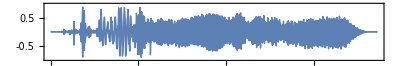

```mathematica
AudioPlot[car]
```

```mathematica
maxcar=AudioLocalMeasurements[car,"Max"]
```

TimeSeries[…]

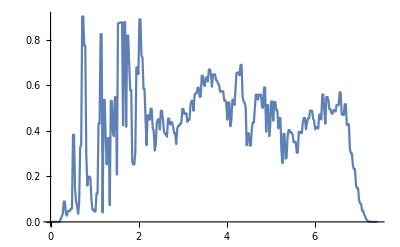

```mathematica
ListLinePlot[maxcar]
```

### Example 3: Analysis of audio signals captured by smart phone

The following example links students’ smart phones to Mathematica. Specifically, an audio signal was captured by an iPhone with an App named SpectrumView, the data then is downloaded to this local computer for visualization. The beauty of this example is that every student can have a wide degree of freedom in choosing their sound object based on his/her own interest. In addition, there will be almost no limitation in when or where a sound signal can be captured. For instance, a student interested in a musical instrument, he/she can then use the App to get the data at any time and any where. A student could also bring the smart phone to a concert hall, as an example to capture the signal then analysis it to understand the acoustics of the concert hall space.

```mathematica
capturebyphone=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/Recording 2019-07-04 09-22-43.wav"]
```

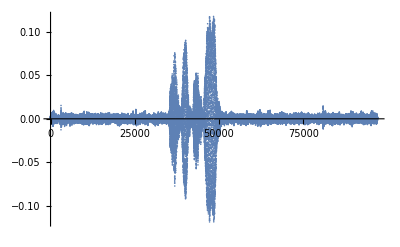

```mathematica
ListPlot[AudioData[capturebyphone],PlotRange->All]
```

The following plot shows the Periodogram of the capture signal, which can be very useful for the study of characteristic frequencies of a particular space.

```mathematica
Manipulate[
Periodogram[capturebyphone,width], {width,100, 8000,1},SaveDefinitions->True]
```

### Example 3’: This is an extension of example 3: Analysis of audio signals from an air tube

For individuals who are more advanced in physics, this example gives an excellent demonstration of studies of resonance frequencies of a system. The audio signals from a Wolfram water bottle, which everyone at this summer school has, are captured via SpectrumView, then analysed using Mathematica. Theoretically for an half closed air of length about 0.3 (m), the lowest resonance frequency is about speed of sound(340m/s)/wavelength(4x0.3(m)), which equals 280 (Hz), and the second lowest resonance frequency is 3x280, 850 (Hz). The smart phone captured data analysis shows peals near these frequencies, as ine can see from below.

```mathematica
Wolframwaterbottleaudio=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/Recording 2019-07-09 11-46-53.wav"]
```

```mathematica
Manipulate[
Periodogram[Wolframwaterbottleaudio,width], {width,50, 2000,10},SaveDefinitions->True]
```